### Plot for spinZeroBoseCondensation.tex (final exam reflection, problem 2)

```mathematica
Manipulate[
Plot[1 - a x^3, {x, 0, 2},
AxesLabel -> {T/Subscript[T, c], Subscript[n, 0]/n}],{a,0.5,1}
]
```

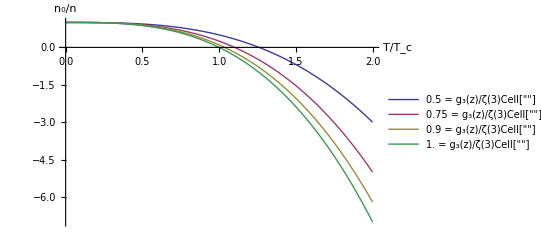

```mathematica
Clear[p]
p = Module[
{a},
a = {0.5, 0.75, 0.9, 1.0} ;
Plot[Evaluate[(1 - # x^3) &/@ a], {x, 0, 2},
AxesLabel -> {T/Subscript[T, c], Subscript[n, 0]/n},
PlotLegends -> Placed[ # Text[" = g_3(z)/ζ(3)Cell[""]"   ] &/@ a, {Left,Bottom}]
]
]
```

```mathematica
<<peeters`
```

peeters`

```mathematica
peeters`exportForLatex["spinZeroBoseCondensationFig1", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/spinZeroBoseCondensationFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/spinZeroBoseCondensationFig1pn.png}

```mathematica
SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit